1. Построить графики функции вероятности возникновения хотя бы одной
 коллизии    (См. Л[1], п.3.6)    в зависимости от числа k экспериментов извлечения с возвратом элементов множества, для множеств с количеством элементов n равным 100+N, 365, 900+N (См. Л[2], п. 8.1-8.2).

104

365

904

1-ⅇ^(-((-1+k0) k0)/(2 n0))

1-1/ⅇ^(2475/52)

1-1/ⅇ^(990/73)

1-1/ⅇ^(2475/452)

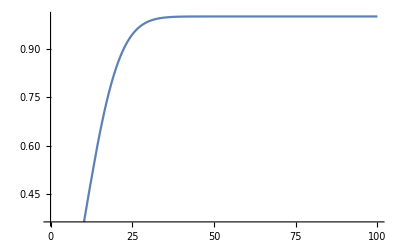

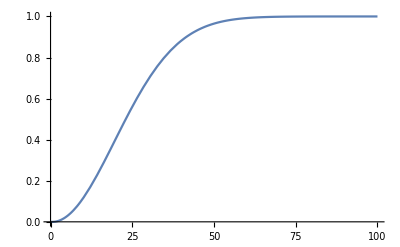

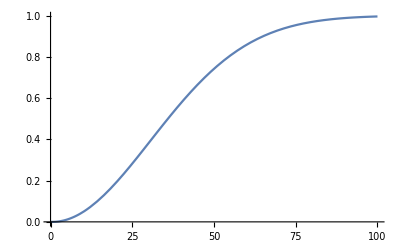

```mathematica
n1=104
n2=365
n3=904
P[k0_, n0_]=Module[{},
res=1-Exp[-k0*(k0-1)/(2*n0)];
res
]
P[100,n1]
P[100,n2]
P[100,n3]
Plot[P[x, n1],{x,0,100}]
Plot[P[x, n2],{x,0,100}]
Plot[P[x, n3],{x,0,100}]
```

2. Объединить три графика и построить там же линию с ординатой равной  0.5.

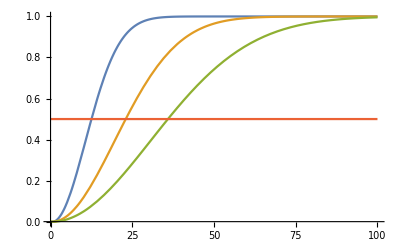

```mathematica
Plot[{P[x, n1],P[x, n2],P[x, n3],x=0.5},{x,0,100}]
```

3. Определить число экспериментов, при котором коллизия появляется с вероятностью 0.5 путем прямого решения уравнения  P(k,n) = 0.5 для трех значений n = 100+N, 365, 900+N (См. Л[2], п. 5.5.4) . Сравнить полученные результаты с расчетом по приближенной формуле k  1.1774n.
3. Определить число экспериментов, при котором коллизия появляется с вероятностью 0.99 для n = 100+N, 365, 900+N.

```mathematica
Solve[P[x,n1]==0.5]
Solve[P[x,n2]==0.5]
Solve[P[x,n3]==0.5]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-11.5177},{x→12.5177}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-21.9999},{x→22.9999}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-34.9042},{x→35.9042}}

3. Определить число экспериментов, при котором коллизия появляется с вероятностью 0.99 для n = 100+N, 365, 900+N.

```mathematica
Solve[P[x,n1]==0.99]
Solve[P[x,n2]==0.99]
Solve[P[x,n3]==0.99]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-30.4536},{x→31.4536}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-57.483},{x→58.483}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-90.7491},{x→91.7491}}

4. Найти предел, к которому стремится вероятность хотя бы одной коллизии при числе экспериментов, стремящихся к бесконечности (См. Л[2], п. 5.4).

```mathematica
Limit[P[x,n1],x->Infinity]
Limit[P[x,n2],x->Infinity]
Limit[P[x,n3],x->Infinity]
```

1

1

1

5. Установить генератор случайных чисел в начальное состояние но номеру в списке группы N и сформировать список из 15 случайных целых чисел, которые лежат в интервале от 10+N до 25+N.

```mathematica
RandomSeed[4]
range=RandomInteger[{14,29},15]
```

RandomSeed[4]

{28,15,15,25,25,27,21,18,22,24,15,18,17,20,27}

6. С помощью функции Union[] исключить повторяющиеся элементы и определить число коллизий, как разницу между длинами исходного списка и списка без повторений.

```mathematica
unrange=Union[range]
kol=Length[range]-Length[unrange]
```

{15,17,18,20,21,22,24,25,27,28}

5

7. Подготовить список, состоящий из 0, длиной 10000+1000*N - с помощью функции Table[] (См. Л[2], п. 4.1.2).

```mathematica
zeros=Table[0*i,{i,1,14000}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,13866,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

8. На подмножестве целых чисел от 1 до 365 реализовать случайную многократную выборку по 23 элемента и для каждой выборки определить число коллизий. 
Число повторов эксперимента равно 10000+1000*N.
 Операцию циклических вычислений выполнить с помощью функций (См. Л[2], п. 2.6,2.7), указанных в  таблице ( вариант реализации определяется из следующего соотношения nv = N(mod3)+1 ) :
Номер варианта nv	1	2	3
Оператор	Do	While	For

```mathematica
intrange=Range[365]
n=1; While[n<=14000,{r=RandomChoice[intrange, 23],zeros[[n]]=Length[r]-Length[Union[r]]};n++]
zeros
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365}

{3,1,3,0,1,2,1,0,0,1,0,1,1,0,1,0,1,2,0,1,2,1,1,1,1,1,0,0,1,2,2,0,0,0,0,2,1,0,1,1,1,1,0,1,0,1,0,0,2,0,0,4,0,1,1,0,0,1,0,0,1,1,2,2,2,3,0,13866,0,2,0,1,0,0,1,0,1,0,0,1,1,0,1,0,2,0,1,0,0,2,1,3,0,1,1,0,0,1,0,1,1,0,0,1,0,1,0,2,2,1,0,0,1,0,0,0,1,0,0,0,0,0,3,0,2,1,0,0,1,1,1,0,0,1,1}
 |  |  |  |

9. Определить число экспериментов без коллизий, с одной, двумя коллизиями и т.д., используя функцию Tally[].

```mathematica
tal=Tally[zeros]
```

{{3,325},{1,5150},{0,6915},{2,1578},{4,30},{5,2}}

10. Построить гистограмму распределения вероятности коллизий, используя функцию Histogram[] со следующими параметрами: число столбцов гистограммы (bin) равно длине списка из п.8; вид гистограммы определяется спецификацией “Probability.

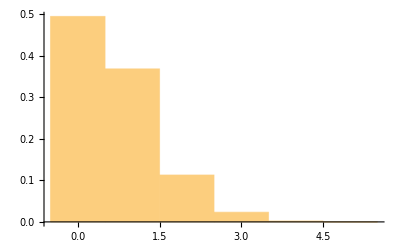

```mathematica
Histogram[zeros,Length[tal],"Probability",PlotRange->Automatic]
```